```mathematica
(*1a Make a plot of the (h,r)plane.*)
f:=x*r-x^2+h; 
df=D[f,x];
xsolution=Solve[df==0,x];
fsolution = f/. {xsolution}
hsolution=Solve[{fsolution}==0,{h}]; (*få ut svaret på h=*)
sol=hsolution[[All,1,2]]  ;
p1 = Plot[ sol[[1]], {r,-10,10},PlotRange->{-25,10}, AxesLabel->{r,h} ]
```

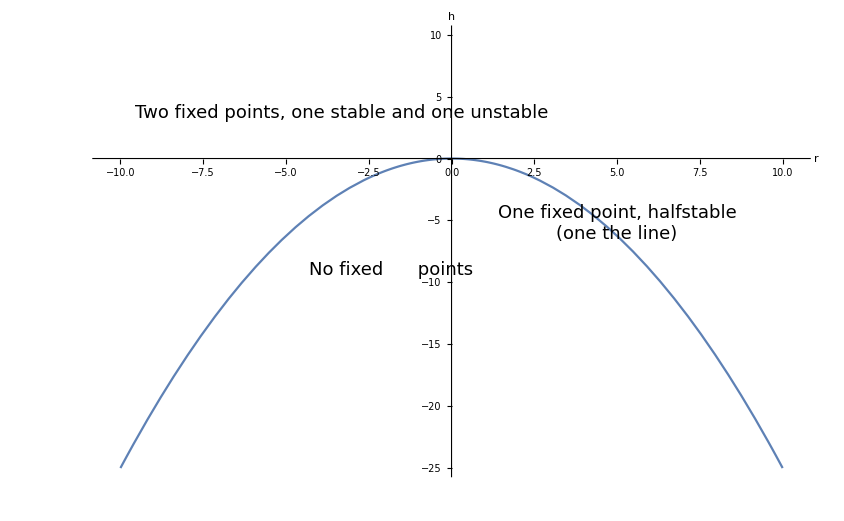

```mathematica
(*1b Make a three-dimensional (x*,h,r)-plot of the surface of fixed points*)
f2=h+x (r-x);
x2solution=Solve[f2==0,x];
x2 = x2solution[[All,1,2]];
p2 = ParametricPlot3D[{{r,h,x2[[2]]},{r,h,x2[[1]]}}, {r, -3,3}, {h,-3,3}, PlotLegends->{"Positive roots", "Negative roots"}, AxesLabel->{r,h,x}]
(*using export instead to include the legends with the plot*)
(*Export["exportp2.png",p2]*)
```

-Graphics3D-

```mathematica
(*1c*)(*Write[h_c(r),r] depending on r*)(*This answer is calculated above and obtained from the variable "sol" which is = -r^24 *)
sol
```

{-r^2/4}

```mathematica
(*1d*)
(*Similarly,for each point,[h_c(r),r],on the bifurcation curve,a transcritical bifurcation occurs in one direction that depends on r. Find this direction analytically*)
(*To obtain the value we can derive the answer in 1.1c and normalize it*)
```

```mathematica
dh=D[sol[[1]],r];
Normalize[{dh,1}]
```

{-r/(2 √(1+Abs[r]^2/4)),1/(√(1+Abs[r]^2/4))}